# Moments of the lattice An

## The G recursion

```mathematica
Clear[G];
G[n_,0,0]:=1;
G[1,k_,m_]:=
1/(2*k +m+1);
G[n_,k_,m_]:=G[n,k,m]=Sum[Sum[Binomial[k,j]*Binomial[m,jd]*1/(2*j +jd+1)*G[n-1,k-j,m-jd],{jd,0,m}],{j,0,k}];
```

```mathematica
G[3,2,2]
```

1235/252

## The moment coefficient

```mathematica
Clear[Mc];
Mc[n_,m_]:=Mc[n,m]=Sum[Sum[Sum[Binomial[m,k]*(1-1/(n+1))^k*Multinomial[j1,j2,m-k-j1-j2]*(-1/(n+1))^(m-k-j1)*2^j2*G[n-1,j1,j2+2*(m-k-j1-j2)],{j2,0,m-k-j1}],{j1,0,m-k}],{k,0,m}];
```

```mathematica
Mc[5,3]/Factorial[3]
```

1177/13608

```mathematica
Mc[2,2]
```

14/45

## The moment

```mathematica
eucpower[n_,m_]:=n*Sqrt[n+1]*Mc[n,m]/(n+2*m);
```

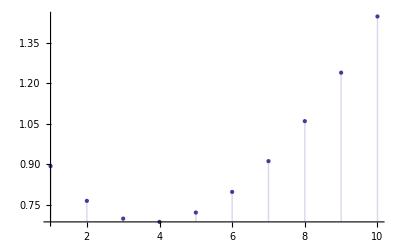

{0.0346478,0.0945982,0.212717,0.419295,0.752256,1.25762,1.98999,3.01298,4.39965}

```mathematica
DiscretePlot[Log[eucpower[8,m]], {m,1,10}]
Table[N[eucpower[n,4]],{n,2,10}]
```

## The probability of error

```mathematica
Pe[n_,v_,t_] :=1 - Sum[(-1)^m/2^m/v^m/Factorial[m]*eucpower[n,m],{m,0,t}]/(2*Pi*v)^(n/2);
N[Pe[2,10/100,33]]
```

0.0652598

## Plotting the probability of error versus SNR

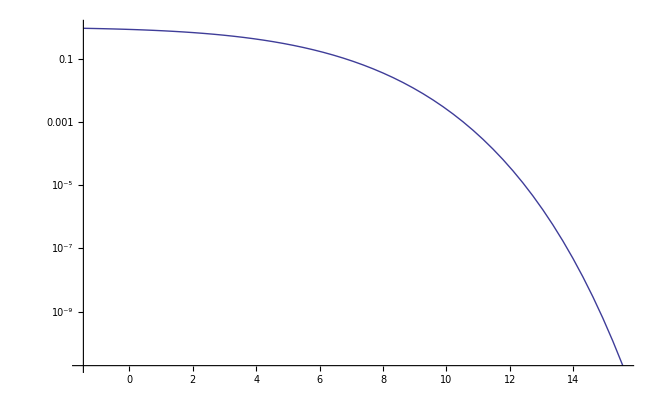

```mathematica
n = 8;
V = Sqrt[n+1];
vars = Table[1/2*(93/100)^k, {k,0,56}];
snrdb = 10*Log10[V^(2/n)/(4#)] &/@ vars;
pes = Pe[n,#,400]&/@ vars;
ListLogPlot[Thread[{ snrdb,pes }],Joined->{True}]
```

Execute below to write the result to a file suitable for making a metapost plot.

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]]
fname = FileNameJoin[{Directory[],"/Software/An_lattice_error_probability/plots/pe" <> ToString[n]}]
str = OpenWrite[fname]
Do[WriteString[str, ToMetaPostString[N[snrdb[[k]]]] <> "\t"  <> ToMetaPostString[N[pes[[k]]]]  "\n"],{k,Length[pes]}]
Close[str]
FilePrint[%]
```

/home/mckillrg/Software/An_lattice_error_probability/plots/pe5

OutputStream[/home/mckillrg/Software/An_lattice_error_probability/plots/pe5,25]

/home/mckillrg/Software/An_lattice_error_probability/plots/pe5

-1.454e0	9.18099e-1
 -1.13883e0	9.05545e-1
 -8.23656e-1	8.91358e-1
 -5.08486e-1	8.75394e-1
 -1.93315e-1	8.57516e-1
 1.21855e-1	8.37591e-1
 4.37026e-1	8.15504e-1
 7.52196e-1	7.91158e-1
 1.06737e0	7.64484e-1
 1.38254e0	7.35451e-1
 1.69771e0	7.04068e-1
 2.01288e0	6.70396e-1
 2.32805e0	6.34552e-1
 2.64322e0	5.9672e-1
 2.95839e0	5.57149e-1
 3.27356e0	5.16155e-1
 3.58873e0	4.74123e-1
 3.9039e0	4.31497e-1
 4.21907e0	3.88772e-1
 4.53424e0	3.46477e-1
 4.84941e0	3.0516e-1
 5.16458e0	2.65365e-1
 5.47975e0	2.27608e-1
 5.79492e0	1.92353e-1
 6.11009e0	1.5999e-1
 6.42527e0	1.30813e-1
 6.74044e0	1.05011e-1
 7.05561e0	8.26553e-2
 7.37078e0	6.37008e-2
 7.68595e0	4.79973e-2
 8.00112e0	3.53021e-2
 8.31629e0	2.53032e-2
 8.63146e0	1.76429e-2
 8.94663e0	1.19444e-2
 9.2618e0	7.836e-3
 9.57697e0	4.97083e-3
 9.89214e0	3.04216e-3
 1.02073e1	1.79182e-3
 1.05225e1	1.01308e-3
 1.08377e1	5.48293e-4
 1.11528e1	2.83212e-4
 1.1468e1	1.39171e-4
 1.17832e1	6.48371e-5
 1.20983e1	2.85317e-5
 1.24135e1	1.1812e-5
 1.27287e1	4.58079e-6
 1.30438e1	1.65634e-6
 1.3359e1	5.55611e-7
 1.36742e1	1.71964e-7
 1.39894e1	4.88206e-8
 1.43045e1	1.26332e-8
 1.46197e1	2.95942e-9
 1.49349e1	6.23203e-10
 1.525e1	1.17014e-10
 1.55652e1	1.95558e-11